```mathematica
temps=Import["~/Documents/flicker/temps/1017_temperatures.tsv"];
```

```mathematica
sun=Import["~/Documents/flicker/temps/1017_sunlight.tsv"];
```

The data doesn't start until a certain point, so we start our analysis there:

```mathematica
HoldsUntil[xs_,crit_]:=Block[{i=1},While[i≤Length[xs]&&crit[xs⟦i⟧],i++];i]
```

```mathematica
start=Max[HoldsUntil[temps,Length[#1]≠25&],HoldsUntil[sun,Length[#1]≠25&]];
```

```mathematica
temps=temps⟦start;;All⟧;sun=sun⟦start;;All⟧;
```

### Phase Delay

#### Daily

```mathematica
mtemps=Mean/@(Select[#1,NumericQ]&)/@Transpose[Select[(#1⟦2;;All⟧&)/@temps,Length[#1]==24&]];
```

```mathematica
msun=Mean/@(Select[#1,NumericQ]&)/@Transpose[Select[(#1⟦2;;All⟧&)/@sun,Length[#1]==24&]];
```

We predict a π/4 phase delay, when we run a list correlation over time series data, which manifests itself as a shift in a sin-like curve which may be observed when we look at the correlation between the sunlight data (which we assume measures excitation) and the temperature fluctuations it is thought to cause.

```mathematica
dphasef=Interpolation[MapIndexed[{1/24 (#2⟦1⟧-1) 2 π,#1}&,ListCorrelate[mtemps,msun,1]]];
```

```mathematica
dphase=x/.NMaximize[{dphasef[x],0≤x≤(23 2 π)/24},x]⟦2⟧;
```

```mathematica
dphase
```

5.62267

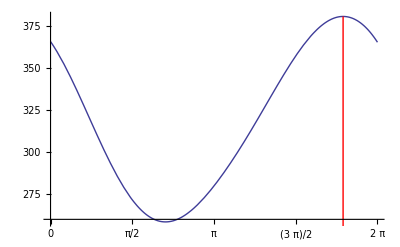

```mathematica
Show[Plot[dphasef[x],{x,0,2 π},Ticks->{Table[(i 2 π)/8,{i,0,8}],Automatic}],Graphics[{Red,Line[{{dphase,0},{dphase,dphasef[dphase]}}]}]]
```

#### Yearly

```mathematica
ytemps=Transpose[Partition[PadRight[(#1⟦2;;All⟧&)/@temps,(Floor[Length[temps]/365]+1) 365,{{"X"}}],365]];
```

```mathematica
yytemps=(Mean[Flatten[#1]]&)/@(Select[#1,Length[#1]==24&]&)/@Map[Select[#1,NumericQ]&,ytemps,{2}];
```

```mathematica
ysun=Transpose[Partition[PadRight[(#1⟦2;;All⟧&)/@sun,(Floor[Length[sun]/365]+1) 365,{{"X"}}],365]];
```

```mathematica
yysun=(Mean[Flatten[#1]]&)/@(Select[#1,Length[#1]==24&]&)/@Map[Select[#1,NumericQ]&,ysun,{2}];
```

We predict a π/4 phase delay in yearly variation as well.  As we can see from the data, this delay is shorter for some unknown reason.

```mathematica
yphasef=Interpolation[MapIndexed[{1/365 (#2⟦1⟧-1) 2 π,#1}&,ListCorrelate[yytemps,yysun,1]]];
```

```mathematica
yphase=x/.NMaximize[{yphasef[x],0≤x≤((Length[yytemps]-1) 2 π)/Length[yytemps]},x]⟦2⟧;
```

```mathematica
yphase
```

5.92169

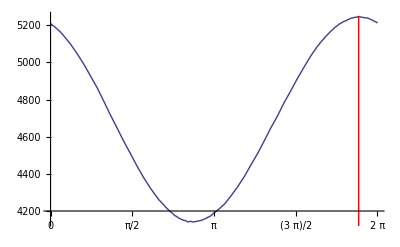

```mathematica
Show[Plot[yphasef[x],{x,0,2 π},Ticks->{Table[(i 2 π)/8,{i,0,8}],Automatic}],Graphics[{Red,Line[{{yphase,0},{yphase,yphasef[yphase]}}]}]]
```

### Flicker Noise

```mathematica
atemps=Flatten[Map[Piecewise[{{#1,NumericQ[#1]}},0]&,(PadRight[#1,24,0]&)/@(#1⟦2;;All⟧&)/@temps,{2}]];
```

```mathematica
powtemps=MapIndexed[{#2⟦1⟧,#1}&,(Abs[Fourier[atemps]]^2)⟦1;;Length[atemps]/2⟧];
```

```mathematica
p1=ListLogLogPlot[powtemps,PlotRange->All,AspectRatio->1];
```

```mathematica
p2=LogLogPlot[Evaluate[Fit[powtemps,{1/x},x]],{x,1,Length[atemps]/2},PlotStyle->{Red},PlotRange->All,AspectRatio->1];
```

When looking at the power spectrum, we expect to see 1/f noise.  it appears that certain periodic signals are perturbing the regression:

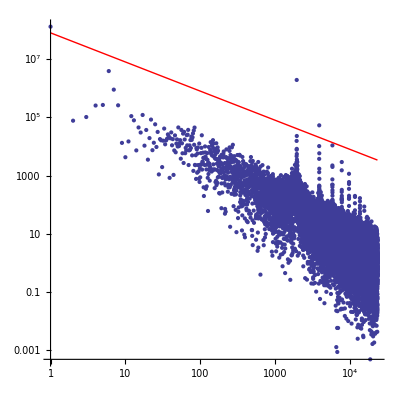

```mathematica
Show[p1,p2]
```

These perturbations seem to correspond to 24 hour cycles:

```mathematica
p3=ListLogPlot[powtemps,PlotRange->All,AspectRatio->1];
```

```mathematica
p4=Graphics[Table[{Red,Line[{{Length[atemps]/24 i,-10},{365,10^7}}]},{i,0,15}]];
```

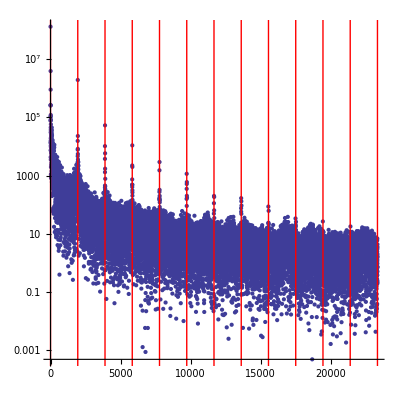

```mathematica
Show[p3,p4]
```

```mathematica
apowtemps=Select[powtemps,24≤Mod[#1⟦1⟧,Length[atemps]/24]≤Length[atemps]/24-24&];
```

```mathematica
p5=ListLogLogPlot[apowtemps,PlotRange->All,PlotStyle->{Green}];
```

```mathematica
p6=LogLogPlot[Evaluate[Fit[apowtemps,{1/x},x]],{x,1,Length[atemps]/2},PlotStyle->{Red},PlotRange->All,AspectRatio->1];
```

The 1/f regression looks much better when we discard the periodic signals:

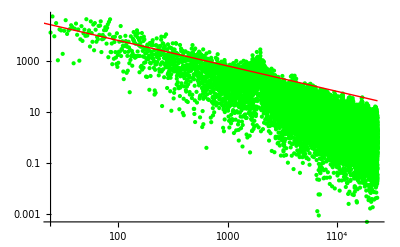

```mathematica
Show[p5,p6]
```

The moving average, corrected for periodic signals, closely matches 1/f noise:

```mathematica
mapowtemps=Select[MovingAverage[powtemps,24],24≤Mod[#1⟦1⟧,Length[atemps]/24]≤Length[atemps]/24-24&];
```

```mathematica
p7=ListLogLogPlot[mapowtemps,PlotRange->All,PlotStyle->{Blue},AspectRatio->1];
```

```mathematica
p8=LogLogPlot[Evaluate[Fit[mapowtemps,{1/x},x]],{x,1,Length[atemps]/2},PlotStyle->{Red},PlotRange->All,AspectRatio->1];
```

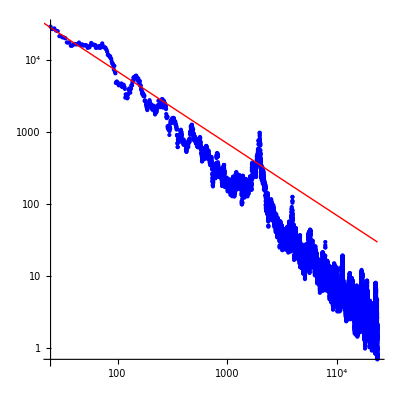

```mathematica
Show[p7,p8]
```